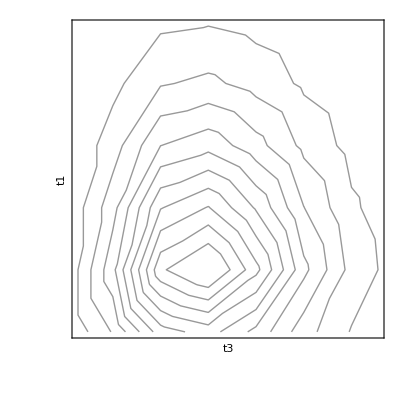

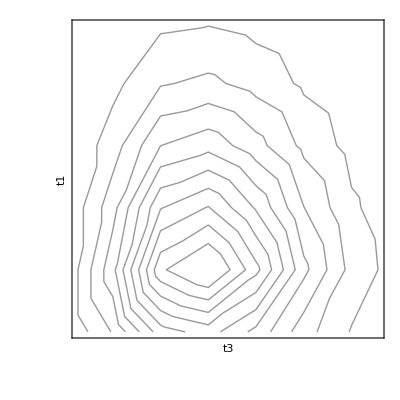

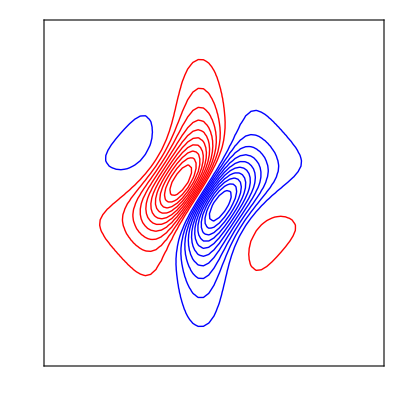

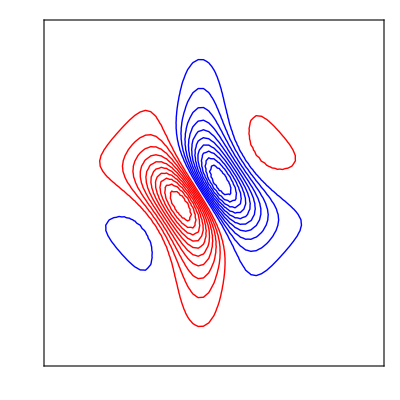

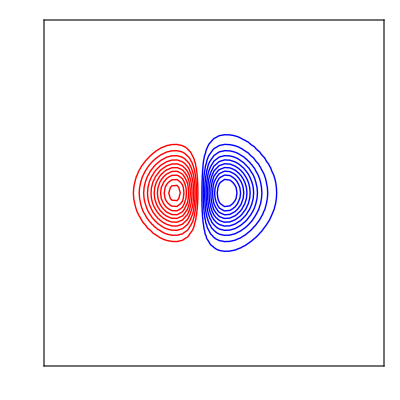

```mathematica
Rnr=(Exp[-I(t3+t1)w]-Exp[-I (t3 (w-Δ)+t1 w)])*Exp[-g[t1]-g[t2]-g[t3]+g[t1+t2]+g[t2+t3]-g[t1+t2+t3]];
Rr=(Exp[-I(t3-t1)w]-Exp[-I(t3 (w-Δ)-t1 w)])*Exp[-g[t1]+g[t2]-g[t3]-g[t1+t2]-g[t2+t3]+g[t1+t2+t3]];
g[t_]=Δw^2 Subscript[τ, c]^2(Exp[-t/Subscript[τ, c]]+t/Subscript[τ, c]-1);
Δ=5;
Δw=5;
Subscript[τ, c]=1;
w=0;
t2=.1;
nt=64;
dt=.1;
Rnrlist=Table[Rnr,{t1,0,(nt-1)*dt,dt},{t3,0,(nt-1)*dt,dt}];
Rrlist=Table[Rr,{t1,0,(nt-1)*dt,dt},{t3,0,(nt-1)*dt,dt}];
For[i=1,i≤nt,i++,Rnrlist[[i,1]]/=2;Rrlist[[i,1]]/=2];
For[i=2,i≤nt,i++,Rnrlist[[1,i]]/=2;Rrlist[[1,i]]/=2];
ListContourPlot[Re[Rrlist], PlotRange->All,Contours->10,ContourShading->False,FrameTicks->None,FrameLabel->{t3,t1}]
ListContourPlot[Re[Rnrlist], PlotRange->All,Contours->10,ContourShading->False,FrameTicks->None,FrameLabel->{t3,t1}]
spectrum2Dr=Fourier[Rrlist];
spectrum2Dr=Reverse[Drop[RotateRight[spectrum2Dr,{nt/2,nt/2}],1,1]];

spectrum2Dnr=Fourier[Rnrlist];
spectrum2Dnr=Drop[RotateRight[spectrum2Dnr,{nt/2,nt/2}],1,1];

spectrum2Dabs=Re[spectrum2Dr+spectrum2Dnr];
max=Max[Max[Re[spectrum2Dr]],-Min[Re[spectrum2Dr]]];
p1=ListContourPlot[Re[spectrum2Dr], PlotRange->{0,max},ContourShading->False,Contours->10,Ticks->None,ContourStyle->{RGBColor[0,0,1]},DisplayFunction->Identity];
p2=ListContourPlot[Re[spectrum2Dr], PlotRange->{-max,0},ContourShading->False,Contours->10,Ticks->None,ContourStyle->{RGBColor[1,0,0]},DisplayFunction->Identity];
Show[{p1,p2},PlotRange->{{1,nt-1},{1,nt-1}},FrameTicks->{None,None},DisplayFunction->$DisplayFunction]
max=Max[Max[Re[spectrum2Dnr]],-Min[Re[spectrum2Dnr]]];
p1=ListContourPlot[Re[spectrum2Dnr], PlotRange->{0,max},ContourShading->False,Contours->10,Ticks->None,ContourStyle->{RGBColor[0,0,1]},DisplayFunction->Identity];
p2=ListContourPlot[Re[spectrum2Dnr], PlotRange->{-max,0},ContourShading->False,Contours->10,Ticks->None,ContourStyle->{RGBColor[1,0,0]},DisplayFunction->Identity];
Show[{p1,p2},PlotRange->{{1,nt-1},{1,nt-1}},FrameTicks->{None,None},DisplayFunction->$DisplayFunction]
max=Max[Max[Re[spectrum2Dabs]],-Min[Re[spectrum2Dabs]]];
p1=ListContourPlot[Re[spectrum2Dabs], PlotRange->{0,max},ContourShading->False,Contours->10,Ticks->None,ContourStyle->{RGBColor[0,0,1]},DisplayFunction->Identity];
p2=ListContourPlot[Re[spectrum2Dabs], PlotRange->{-max,0},ContourShading->False,Contours->10,Ticks->None,ContourStyle->{RGBColor[1,0,0]},DisplayFunction->Identity];
Show[{p1,p2},PlotRange->{{1,nt-1},{1,nt-1}},FrameTicks->{None,None},DisplayFunction->$DisplayFunction]
```